# Práctica 2.2

## Alumnos: Sergi Albiach Caro & Stéphane Díaz-Alejo León

## Ejercicios

```mathematica
afd1={{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}};
```

1.-Implemente un módulo en Mathematica que, tomando como entrada un AFD proporcione como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD mediante entrada paralela.

```mathematica
AFDaACUU[AFD_]:=Module[{S,Smas,f,i,j,k, result},
S=AFD[[1]]∪AFD[[2]];(* S=Q∪∑ *)
Smas=AFD[[5]]; (* S^+=F *)

f=AFD[[3]];

(* Insertar transiciones {a,b,b} ∀a,b∈∑ & {q,p,p} ∀q,p∈Q *)
For[k=1,k≤2,k++,
For[i=1,i≤Length[AFD[[k]]],i++,
For[j=1,j≤Length[AFD[[k]]],j++,
AppendTo[f,{AFD[[k,i]],AFD[[k,j]],AFD[[k,j]]}];
];
];
];

result={S,f,Smas};
Return[result];
];
```

```mathematica
ACU=AFDaACUU[afd1]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

2.-Implemente un módulo Mathematica que, tomando como entrada una cadena arbitraria, un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de frontera q∈S, proporcione como salida True si el AC acepta la cadena y False en caso contrario.

```mathematica
ACCadena[cadena_,AC_,frontera_]:=Module[{res,i,j,aux},
res=cadena;
For[i=1,i≤Length[res],i++,
aux={Cases[AC[[2]],{frontera,res[[1]],_}][[1,3]]};
For[j=1,j≤Length[res]-1,j++,
AppendTo[aux,Cases[AC[[2]],{res[[j]],res[[j+1]],_}][[1,3]]];
];
res=aux;
];
Return[MemberQ[AC[[3]],res[[Length[cadena]]]]];
];
```

```mathematica
ACCadena[{a,b,a,a,b},ACU,q]
```

True

3.-Proporcione una construcción formal para obtener a partir de un AFD, un AC equivalente unidimensional bidireccional (vecindario{-1,0,1}) con entrada paralela. Implemente un módulo en Mathematica que lleve acabo la construcción propuesta.

Construcción formal: convertir transiciones {vec izq, cel, nuevo est} en {vec izq, cel, vec der, nuevo est}, ∀vec der∈S

```mathematica
AFDaACUB[AFD_]:=Module[{res,f,i,j},
res=AFDaACU[AFD];

(* Convertir transiciones {vec izq, cel, nuevo est} en {vec izq, cel, vec der, nuevo est}, ∀vec der∈S *)
f={};
For[i=1,i≤Length[res[[2]]],i++,
For[j=1,j≤Length[res[[1]]],j++,
AppendTo[f,{res[[2,i,1]],res[[2,i,2]],res[[1,j]],res[[2,i,3]]}];
];
];
res[[2]]=f;
Return[res];
];
```

```mathematica
AFDaACUB[afd1]
```

{{a,b,p,q,r},{{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r},{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b}},{r}}

4.-Implemente un módulo Mathematica que muestre la secuencia de computación que se lleva acabo en el módulo propuesto en la actividad (2) mediante un diagrama espacio-temporal. (Nota: Utilice las funciones ArrayPlot y ListAnimate explicados en la práctica de Fundamentos Básicos).

```mathematica
ACCadenaPlot[cadena_,AC_,frontera_]:=Module[{res,i,j,aux},
res={cadena};
For[i=1,i≤Length[cadena],i++,
aux={Cases[AC[[2]],{frontera,res[[1,1]],_}][[1,3]]};
For[j=1,j≤Length[res[[1]]]-1,j++,
AppendTo[aux,Cases[AC[[2]],{res[[1,j]],res[[1,j+1]],_}][[1,3]]];
];
PrependTo[res,aux];
];
Return[res];
];
 ACCadenaPlot2[cadena_,AC_,frontera_]:=Module[{res,i,j,aux},
res={cadena};
For[i=1,i≤Length[cadena],i++,
aux={Cases[AC[[2]],{frontera,res[[1,1]],_}][[1,3]]};
For[j=1,j≤Length[res[[1]]]-1,j++,
AppendTo[aux,Cases[AC[[2]],{res[[1,j]],res[[1,j+1]],_}][[1,3]]];
];
PrependTo[res,aux];
];

res=ConvertirNum[res];

Return[ArrayPlot[res,ColorFunction->"Rainbow",Mesh->True]];
];
ConvertirNum[lista_]:=Module[{i, res,cadena,j,aux},
res={};

For[i=1,i≤Length[lista],i++,
cadena=lista[[i]];
aux={};
For[j=1,j≤Length[cadena],j++,
AppendTo[aux,ToCharacterCode[ToString[cadena[[j]]]]];
];

AppendTo[res,Flatten[aux]];
];

Return[res];
];
```

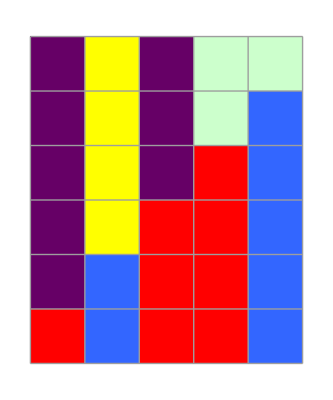

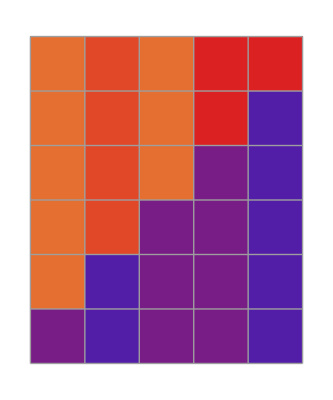

```mathematica
ArrayPlot[ACCadenaPlot[{a,b,a,a,b},ACU,q],ColorRules->{a->Red,b->RGBColor[0.2,0.4,1],q->Yellow,p->RGBColor[0.4,0,0.4],r->RGBColor[0.8,1,0.8]},Mesh->True]
ACCadenaPlot2[{a,b,a,a,b},ACU,q]
```